# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Entropy

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Entropy\\packages\\QMB.wl"];
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Entropy\\packages\\Chaometer.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
```

# Method

## Random product state

```mathematica
?IsingNNOpenHamiltonian
```

```mathematica
L=8;
hx=J=1.;
hz=1.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
Clear[U];
U[t_]:=MatrixExp[-I*H*t];
```

```mathematica
random=haar[L];
```

```mathematica
tlist=Range[0,50,0.1];
```

```mathematica
randomt=ParallelTable[StateEvolution[t,random,eigenval,eigenvec],{t,tlist}];
```

```mathematica
densityrandomt=ParallelTable[Dyad[i,i],{i,randomt}];
```

```mathematica
reducedrandomt=Table[MatrixPartialTrace[i,2,{2^(L/2),2^(L/2)}],{i,densityrandomt}];
```

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
```

```mathematica
eigenreducedrandomt=ParallelTable[Sort[Eigenvalues[Chop[i]]],{i,reducedrandomt}];
```

```mathematica
entropies=ParallelTable[Total[Map[VNentropy,i]],{i,eigenreducedrandomt}];
```

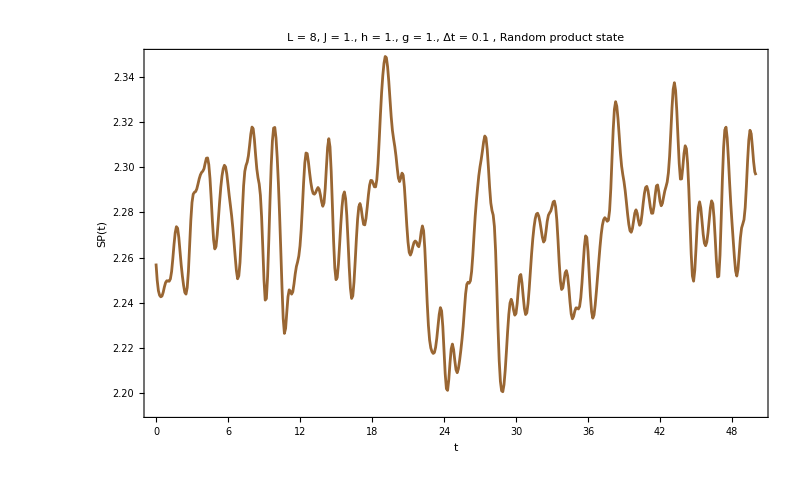

```mathematica
ListPlot[Transpose[{tlist,entropies}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx]<>", g = "<>ToString[hz]<>", Δt = 0.1 , Random product state",20,Black],PlotStyle->{Brown},ImageSize->800,PlotLegends->Style["Svn(t)",Black,20],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

## Eigenvectors for h = 0

```mathematica
L=8;
hx=0;
J=1.;
hz=1.0;
Htest=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvaltest,eigenvectest}=Transpose[Sort[Transpose[Eigensystem[N[Htest]]]]];
```

```mathematica
L=8;
hx=1;
J=1.;
hz=1.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
energytest=ParallelTable[Chop[i.H.i],{i,eigenvectest}];
```

```mathematica
sortedEigenvectors=SortBy[Transpose[{energytest,eigenvectest}],First][[All,2]];
```

```mathematica
basischangeb=ParallelTable[Conjugate[eigenvec].i,{i,sortedEigenvectors}];
```

```mathematica
iprtestb=ParallelTable[Total[Abs[i]^4],{i,basischangeb}];
```

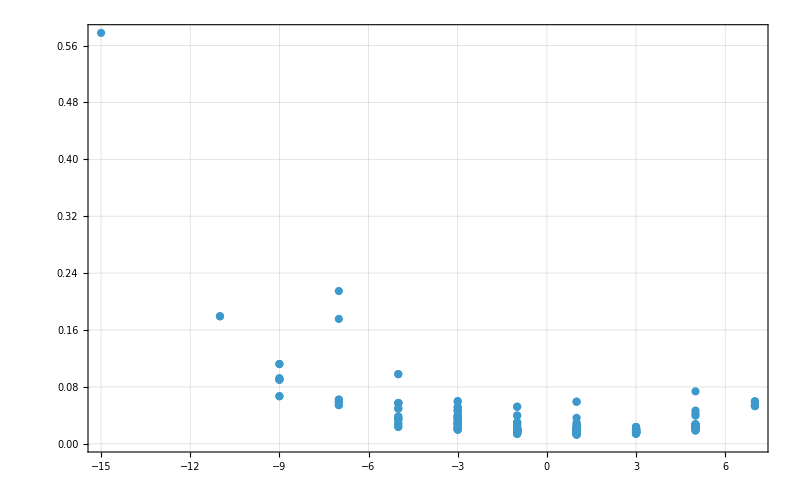

```mathematica
ListPlot[Transpose[{Sort[energytest],iprtestb}],PlotRange->All,PlotTheme->"Detailed",ImageSize->800]
```

## Eigenvectors for h = 0

```mathematica
L=8;
hx=0;
J=1.;
hz=1.0;
Htest=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvaltest,eigenvectest}=Transpose[Sort[Transpose[Eigensystem[N[Htest]]]]];
```

```mathematica
L=8;
hx=1;
J=1.;
hz=1.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
tlist=Range[0,50,0.1];
```

```mathematica
test=eigenvectest[[1;;10]];
```

```mathematica
eigenvect=ParallelTable[StateEvolution[t,j,eigenval,eigenvec],{j,test},{t,tlist}];
```

```mathematica
densityrandomt=Table[Dyad[eigenvect[[j,i]],eigenvect[[j,i]]],{j,Length[test]},{i,Length[tlist]}];
```

```mathematica
densityrandomt//Dimensions
```

{10,501,256,256}

```mathematica
reducedrandomt=Table[MatrixPartialTrace[densityrandomt[[j,i]],2,{2^(L/2),2^(L/2)}],{j,Length[test]},{i,Length[tlist]}];
```

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
```

```mathematica
reducedrandomt//Dimensions
```

{10,501,16,16}

```mathematica
eigenreducedrandomt=ParallelTable[Sort[Eigenvalues[Chop[reducedrandomt[[j,i]]]]],{j,Length[test]},{i,Length[tlist]}];
```

```mathematica
eigenreducedrandomt//Dimensions
```

{10,501,16}

```mathematica
entropies=ParallelTable[Total[Chop[Map[VNentropy,eigenreducedrandomt[[j,i]]]]],{j,Length[test]},{i,Length[tlist]}];
```

```mathematica
data=Table[Transpose[{tlist,i}],{i,entropies}];
```

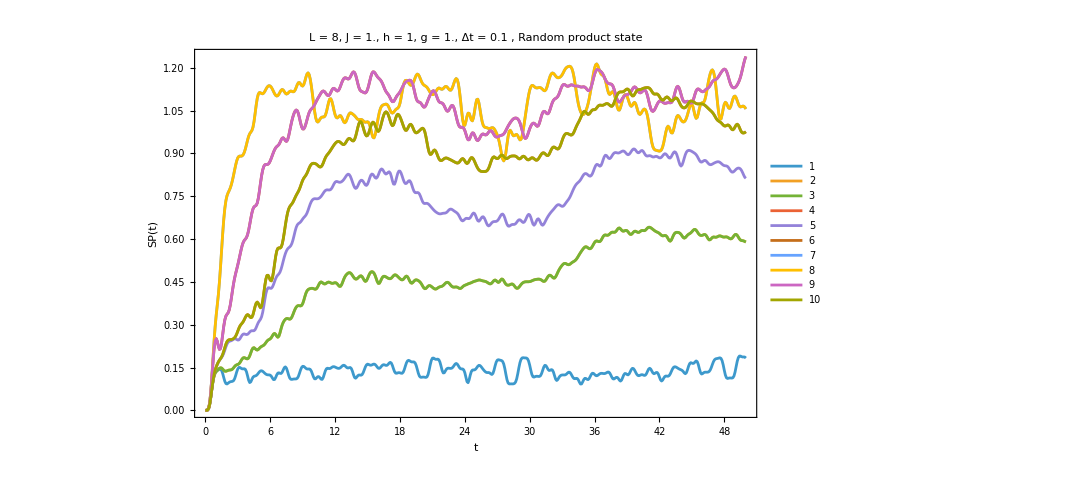

```mathematica
ListPlot[data,PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx]<>", g = "<>ToString[hz]<>", Δt = 0.1 , Random product state",20,Black],ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All,PlotLegends->Automatic]
```